```mathematica
(*-ln(2kr)*)
```

```mathematica
α=2.;u0=1.*10^-8;
V[r_]=-1/r;
k:=√(2e);NegativeLog={};PositiveLog={};
```

```mathematica
e=0.001;
```

```mathematica
Table[
r1=10^logr1;
r2=u0;
sol=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0(*,u'[r1]==k Cos[k r1+δ]*)},u,{r,r1,r2}(*,Method->"ImplicitRungeKutta"*),AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k](*(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,-0.77}];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&];
AppendTo[PositiveLog,{r1,δr}],{logr1,2.5,6,0.1}];
PositiveLog
```

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

{{500,0.913589},{510,0.712152},{520,0.639892},{530,0.616604},{540,0.470846},{550,0.285635},{560,0.203113},{570,0.191008},{580,0.0831974},{590,-0.0868354},{600,-0.188463},{610,-0.199215},{620,-0.264153},{630,-0.411674},{640,-0.533383},{650,-0.560738},{660,-0.58646},{670,-0.698159},{680,-0.830171},{690,-0.890228},{700,-0.896662},{710,-0.960561},{720,-1.0828},{730,-1.17695},{740,-1.19692},{750,-1.2165},{760,-1.30441},{770,-1.41453},{780,-1.47207},{790,-1.47756},{800,-1.51635},{810,1.53012},{820,1.4399},{830,1.40804},{840,1.40243},{850,1.35029},{860,1.258},{870,1.18681},{880,1.16968},{890,1.15952},{900,1.10115},{910,1.01584},{920,0.959338},{930,0.949556},{940,0.935522},{950,0.876164},{960,0.798477},{970,0.751866},{980,0.745361},{990,0.729721},{1000,0.672645},{1500,-0.684331},{2000,-1.42001},{2500,1.26477},{3000,0.943276},{3500,0.71539},{4000,0.539142},{4500,0.398742},{5000,0.285801},{5500,0.19508},{6000,0.118213},{6500,0.0493845},{7000,-0.00677392},{7500,-0.0562684},{8000,-0.101201},{8500,-0.138619},{9000,-0.174548},{10000,-0.233412},{20000,-0.502563},{30000,-0.593697},{40000,-0.639632},{50000,-0.667267},{60000,-0.685745},{70000,-0.698954},{80000,-0.708882},{90000,-0.716593},{100000,-0.722767},{200000,-0.750617},{300000,-0.759914},{400000,-0.764566},{500000,-0.767358},{600000,-0.769219},{700000,-0.770549},{800000,-0.771547},{900000,-0.772323},{316.228,0.827403},{398.107,-0.86805},{501.187,0.887211},{630.957,-0.426337},{794.328,-1.4861},{1000.,0.672645},{1258.93,-0.152917},{1584.89,-0.843966},{1995.26,-1.41897},{2511.89,1.24932},{3162.28,0.866036},{3981.07,0.542917},{5011.87,0.284178},{6309.57,0.0740179},{7943.28,-0.096689},{10000.,-0.233412},{12589.3,-0.342776},{15848.9,-0.431064},{19952.6,-0.501669},{25118.9,-0.558079},{31622.8,-0.60315},{39810.7,-0.639024},{50118.7,-0.667532},{63095.7,-0.690279},{79432.8,-0.708385},{100000.,-0.722767},{125893.,-0.734212},{158489.,-0.743317},{199526.,-0.750552},{251189.,-0.756301},{316228.,-0.760868},{398107.,-0.764499},{501187.,-0.767384},{630957.,-0.769676},{794328.,-0.771497},{1.×10^6,-0.772944}}

```mathematica
PositiveLog=Sort[PositiveLog]
```

{{316.228,0.827403},{398.107,-0.86805},{500,0.913589},{501.187,0.887211},{510,0.712152},{520,0.639892},{530,0.616604},{540,0.470846},{550,0.285635},{560,0.203113},{570,0.191008},{580,0.0831974},{590,-0.0868354},{600,-0.188463},{610,-0.199215},{620,-0.264153},{630,-0.411674},{630.957,-0.426337},{640,-0.533383},{650,-0.560738},{660,-0.58646},{670,-0.698159},{680,-0.830171},{690,-0.890228},{700,-0.896662},{710,-0.960561},{720,-1.0828},{730,-1.17695},{740,-1.19692},{750,-1.2165},{760,-1.30441},{770,-1.41453},{780,-1.47207},{790,-1.47756},{794.328,-1.4861},{800,-1.51635},{810,1.53012},{820,1.4399},{830,1.40804},{840,1.40243},{850,1.35029},{860,1.258},{870,1.18681},{880,1.16968},{890,1.15952},{900,1.10115},{910,1.01584},{920,0.959338},{930,0.949556},{940,0.935522},{950,0.876164},{960,0.798477},{970,0.751866},{980,0.745361},{990,0.729721},{1000,0.672645},{1000.,0.672645},{1258.93,-0.152917},{1500,-0.684331},{1584.89,-0.843966},{1995.26,-1.41897},{2000,-1.42001},{2500,1.26477},{2511.89,1.24932},{3000,0.943276},{3162.28,0.866036},{3500,0.71539},{3981.07,0.542917},{4000,0.539142},{4500,0.398742},{5000,0.285801},{5011.87,0.284178},{5500,0.19508},{6000,0.118213},{6309.57,0.0740179},{6500,0.0493845},{7000,-0.00677392},{7500,-0.0562684},{7943.28,-0.096689},{8000,-0.101201},{8500,-0.138619},{9000,-0.174548},{10000,-0.233412},{10000.,-0.233412},{12589.3,-0.342776},{15848.9,-0.431064},{19952.6,-0.501669},{20000,-0.502563},{25118.9,-0.558079},{30000,-0.593697},{31622.8,-0.60315},{39810.7,-0.639024},{40000,-0.639632},{50000,-0.667267},{50118.7,-0.667532},{60000,-0.685745},{63095.7,-0.690279},{70000,-0.698954},{79432.8,-0.708385},{80000,-0.708882},{90000,-0.716593},{100000,-0.722767},{100000.,-0.722767},{125893.,-0.734212},{158489.,-0.743317},{199526.,-0.750552},{200000,-0.750617},{251189.,-0.756301},{300000,-0.759914},{316228.,-0.760868},{398107.,-0.764499},{400000,-0.764566},{500000,-0.767358},{501187.,-0.767384},{600000,-0.769219},{630957.,-0.769676},{700000,-0.770549},{794328.,-0.771497},{800000,-0.771547},{900000,-0.772323},{1.×10^6,-0.772944}}

```mathematica
FindRoot[u'[r1]/u[r1]==(k-1/(k r1)) Cot[k r1+δ-Log[2 k r1]/k](*(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,1.4}]
```

{δ→1.25364}

```mathematica
AppendTo[NegativeLog,{r1,δ/.%}]
```

{{100.,1.25364}}

{δ→-2.10487}

{{100.,-2.10487}}

```mathematica
PositiveLog=Insert[PositiveLog,{r1,δ/.%},15]
```

ReplaceAll::reps: {100.,-2.10487} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

Insert::ins: 无法在 {{100.,-2.10487}} 中位置 {15} 处插入

Insert[{{100.,-2.10487}},{100.,{δ/.{100.,-2.10487}}},15]

```mathematica
1/(2I)Log[Gamma[1-I/k]/Gamma[1+I/k]]
```

-0.778532+0. ⅈ

```mathematica
(*LogNegativeLog={Log10[NegativeLog[[#]][[1]]],NegativeLog[[#]][[2]]}&/@Range@28;*)
LogPositiveLog={Log10[PositiveLog[[#]][[1]]],PositiveLog[[#]][[2]]}&/@Range@Length[PositiveLog];
```

```mathematica
(*dLogNegativeLog={Log10[NegativeLog[[#]][[1]]],Abs@(NegativeLog[[#]][[2]]+0.7785323639595991)/π}&/@Range@28;*)
dLogPositiveLog={Log10[PositiveLog[[#]][[1]]],Abs@((PositiveLog[[#]][[2]]+0.7785323639595991)/π)}&/@Range@Length[PositiveLog];
```

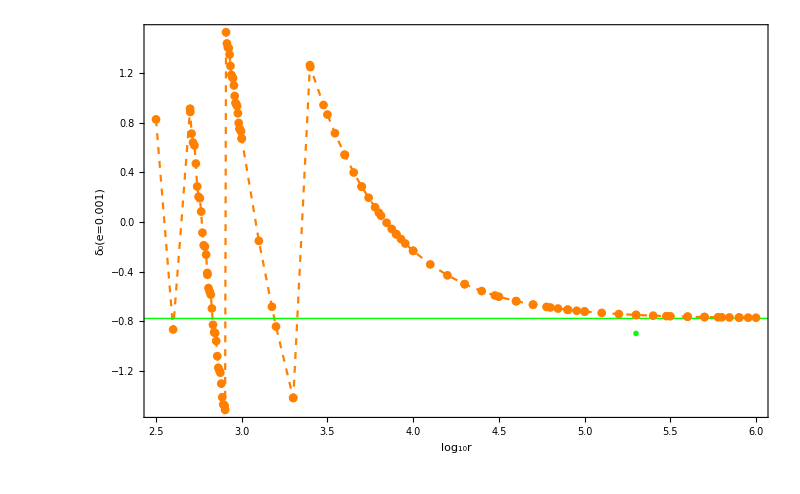

```mathematica
ListPlot[{LogPositiveLog},Frame->True,FrameTicks->{{All,None},{All,None}},Joined->True,PlotMarkers->Automatic,ImageSize->800,FrameLabel->{"log_10r","δ_0(e=0.001)"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Blue}},Epilog->{Green,Thick,InfiniteLine[{0,-0.7785323639595991},{1,0}],Inset[Style["δ_0=-0.778532",15],{5.3,-0.9}]}(*,PlotLegends->{"Negative logarithmic term","Positive logarithmic term"}*)]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_NA_Coulomb_logr1.eps",%];
```

Insert::psl: Insert[{{100.,-2.10487}},{100.,{δ/.{100.,-2.10487}}},15.] 中的位置指定 15. 不是机器整数或者机器整数列表.

General::stop: 在本次计算中，Insert::psl 的进一步输出将被抑制.

Part::partd: 部分指定 15.⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 15.⟦2⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

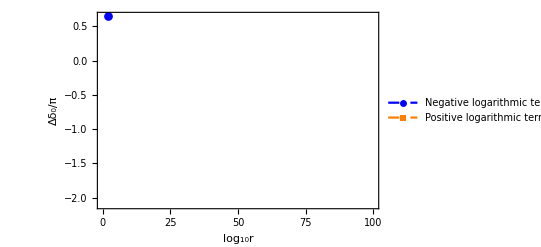

```mathematica
ListPlot[{dLogNegativeLog,dLogPositiveLog},Frame->True,FrameTicks->{{All,None},{All,None}},Joined->True,PlotMarkers->Automatic,ImageSize->Full,FrameLabel->{"log_10r","Δδ_0/π"},RotateLabel->False,PlotStyle->{{Dashed,Blue},{Dashed,Orange}},(*Epilog->{Green,Thick,InfiniteLine[{0,-0.7785323639595991},{1,0}],Inset[Style["δ_0=-0.778532",15],{5.3,-0.9}]},*)PlotLegends->{"Negative logarithmic term","Positive logarithmic term"}]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_NA_Coulomb_bothphasealter_1.eps",%];
```